## Condiciones de regularidad Literatura

```mathematica
Clear[c]
fzgen=PowerExpand[-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+1/(36 2^(1/3) α^2)(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3),Assumptions->{α>0,r>0}]
```

-(-7 r^2 α-36 α^2)/(36 α^2)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+1/(36 2^(1/3) α^2)(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3)

```mathematica
Expand[fzgen]
```

1+(7 r^2)/(36 α)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3))+1/(36 2^(1/3) α^2)(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 c r^2 α^4-27216 r^2 α^5)^2))^(1/3)

### ¿Cómo se comporta f(r) cuando r tiende a Infinito?

```mathematica
FullSimplify[Assuming[r>0&& α>0 ,Simplify[Series[Simplify[fzgen],{r,Infinity,2}]]]]
```

Series::ztest: Unable to decide whether numeric quantities {-7595+378 √2877+54 7^(5/6) √411 (-1085+54 √2877)^(1/3)-1085 (7 (-1085+54 Power[«2»]))^(1/3)-101 (7 (-1085+54 Power[«2»]))^(2/3),7+(7 (-1085+54 √2877))^(1/3)-(101 (7 (-1085+54 Power[«2»]))^(2/3))/(-1085+54 √2877)} are equal to zero. Assuming they are.

1+(-c/3-α/3)/r^2+O[1/r]^(7/3)

```mathematica
Solve[Simplify[-c/3-α/3]==-μ,c]
```

{{c→-α+3 μ}}

```mathematica
c=Simplify[-3*((α/3)-μ)]
```

-α+3 μ

```mathematica
FullSimplify[Assuming[r>0&& α>0 ,Simplify[Series[Simplify[fzgen],{r,Infinity,2}]]]]
```

Series::ztest1: Unable to decide whether numeric quantity 7+(7 (-1085+54 √2877))^(1/3)-(101 (7 (-1085+54 √2877))^(2/3))/(-1085+54 √2877) is equal to zero. Assuming it is.

1-μ/r^2+O[1/r]^(7/3)

Ahora es asintóticamente plano

### ¿Cómo se comporta f(r) cuando r tiende a 0?

```mathematica
Assuming[r>0&& α>0&&μ>0,Simplify[Series[Simplify[fzgen],{r,0,2}]]]
```

1-(7^(1/3) μ r^(2/3))/(2^(2/3) (α μ)^(2/3))+(7 r^2)/(36 α)+O[r]^(7/3)

```mathematica
Expand[fzgen]
```

1+(7 r^2)/(36 α)-(707 r^4)/(18 2^(2/3) (-15190 r^6 α^3-27216 r^2 α^5-27216 r^2 α^4 (-α+3 μ)+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 r^2 α^5-27216 r^2 α^4 (-α+3 μ))^2))^(1/3))+1/(36 2^(1/3) α^2)(-15190 r^6 α^3-27216 r^2 α^5-27216 r^2 α^4 (-α+3 μ)+√(1413572972 r^12 α^6+(-15190 r^6 α^3-27216 r^2 α^5-27216 r^2 α^4 (-α+3 μ))^2))^(1/3)

### Reescalado

```mathematica
Clear[α]
fred=PowerExpand[FullSimplify[fzgen/.r->(Sqrt[(36*α)/7])*r2/.μ->α*μ2,Assumptions->α>0],Assumptions->α>0&&r2∈Reals&&μ2∈Reals]
```

1+r2^2+((-1085 r2^6-(441 r2^2 μ2)/2+3/2 √7 r2^2 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2))^(1/3))/7^(2/3)-(101 (2/7)^(1/3) r2^4)/((-2170 r2^6-441 r2^2 μ2+3 √7 r2^2 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2))^(1/3))

1+r2^2-(101 (2/7)^(1/3) r2^4)/((r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(1/3))+((r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(1/3))/(2^(1/3) 7^(2/3))

### Raíces de f(r)

```mathematica
Simplify[Solve[fred==0,μ2]]
```

$Aborted

### ¿Para qué valores de μ2 f(r) es finita?

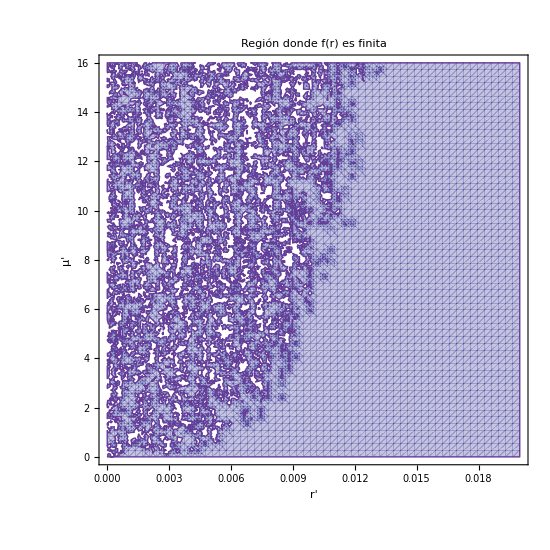

```mathematica
dem:=-2170 r2^6-441 r2^2 μ2+3 √7 r2^2 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)
ffinita=RegionPlot[dem!=0,{r2,0,0.02},{μ2,0,16},PlotPoints->60,Frame->True,FrameStyle->Directive[Black,1.6],FrameTicksStyle->Directive[Black,14],FrameLabel->{Style["r'",20,FontFamily->"Times",Bold],Style["μ'",20,FontFamily->"Times",Bold]},LabelStyle->Directive[16,FontFamily->"Times"],PlotLabel->Style["Región donde f(r) es finita",22,Bold,FontFamily->"Times"],ImageSize->550,PlotTheme->"Classic",BaseStyle->{FontFamily->"Times",16}]
```

```mathematica
Export["Regiones donde f es finita.png",ffinita]
```

Regiones donde f es finita.png

### Gráficas de f(r)

```mathematica
Plot3D[fred,{r2,0,3},{μ2,0,16},PlotRange->All,(*Color fijo usando una escala térmica continua*)ColorFunction->(ColorData["ThermometerColors"][#3]&),ColorFunctionScaling->True,(*Barra de color*)PlotLegends->BarLegend[{"ThermometerColors",{Min[fred],Max[fred]}}],(*Malla desactivada*)Mesh->None,PlotPoints->60,(*Gráficos más grandes*)AxesLabel->{Style["r₂",18,Bold],Style["μ₂",18,Bold],Style["f(r₂)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14]]
```

Power::infy: Infinite expression 1/0.^(1/3) encountered.

-Graphics3D-

Power::infy: Infinite expression 1/0.^(1/3) encountered.

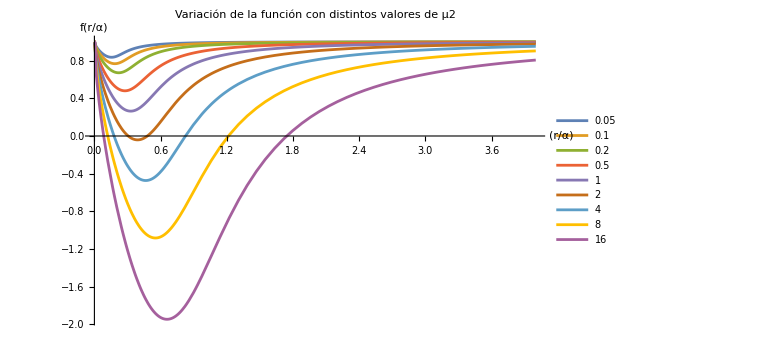

```mathematica
Plot[Evaluate@Table[fred,{μ2,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,3},PlotRange->All,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Variación de la función con distintos valores de μ2",AxesLabel->{Style["(r/α)",18,Bold],Style["f(r/α)",18,Bold],Style["f(r/α)",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14],ImageSize->Large]
```

### Invariante de Kretschman

```mathematica
NN[r_]:=1
f[r_]:=fred
Krt[r2_]=Assuming[r>0&&μ>0,FullSimplify[1/(r2^4 NN[r]^2)(9 r2^4 f'[r]^2 NN'[r]^2+6 r2^4 NN[r] f'[r] NN'[r] f''[r]+NN[r]^2 (12-24 f[r]+12 f[r]^2+6 r2^2 f'[r]^2+r^4 f''[r]^2)+12 r2^4 f[r] f'[r] NN'[r] NN''[r]+4 f[r] NN[r] (3 r2^2 f'[r] NN'[r]+r2^4 f''[r] NN''[r])+4 f[r]^2 (3 r2^2 NN'[r]^2+r2^4 NN''[r]^2))]]
```

(3 (-202 2^(1/3) 7^(2/3) r2^4+14 r2^2 (r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(1/3)+2^(2/3) 7^(1/3) (r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(2/3))^2)/(49 r2^4 (r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(2/3))

```mathematica
Expand[Krt[r2]]
```

-2340/7+(12 (2/7)^(2/3) (r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(1/3))/r2^2+(122412 (2/7)^(2/3) r2^2 (r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(1/3))/(-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2))+(6 (2/7)^(1/3) (r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(2/3))/(7 r2^4)-(2424 (2/7)^(1/3) (r2^2 (-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2)))^(2/3))/(-2170 r2^4-441 μ2+3 √7 √(532656 r2^8+30380 r2^4 μ2+3087 μ2^2))

Power::infy: Infinite expression 1/0.^(2/3) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

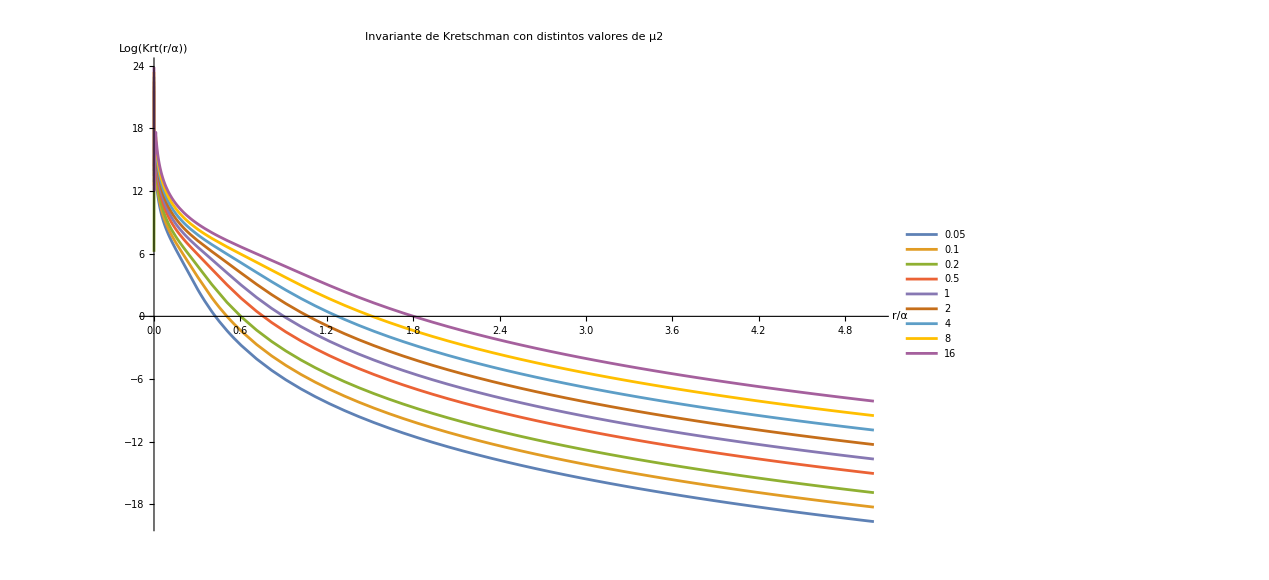

```mathematica
Plot[Evaluate@Table[Log[Krt[r2]],{μ2,{0.05,0.1,0.2,0.5,1,2,4,8,16}}],{r2,0,5},PlotRange->Automatic,MaxRecursion->6,PlotLegends->Placed[{"0.05","0.1","0.2","0.5","1","2","4","8","16"},Right],PlotLabel->"Invariante de Kretschman con distintos valores de μ2",AxesLabel->{Style["r/α",18,Bold],Style["Log(Krt(r/α))",18,Bold],Style["Log(Krt(r/α))",18,Bold]},LabelStyle->Directive[15],TicksStyle->Directive[14]]
```

```mathematica
Assuming[r2>0&&μ2>0,Simplify[Series[Simplify[Krt[r2]],{r2,Infinity,2}]]]
```

Series::ztest1: Unable to decide whether numeric quantity -202 2^(1/3) 7^(2/3)+2 14^(1/3) (-1085+54 √2877)^(2/3)+14 (2 (-1085+54 √2877))^(1/3) is equal to zero. Assuming it is.

O[1/r2]^8

```mathematica
Assuming[r2>0&&μ2>0,Simplify[Series[Simplify[Krt[r2]],{r2,0,2}]]]
```

(36 3^(1/3) μ2^(2/3))/r2^(8/3)-(24 (3^(2/3) μ2^(1/3)))/r2^(4/3)-2340/7+(4904 r2^(4/3))/(7 3^(2/3) μ2^(1/3))+O[r2]^(7/3)